#### Storage cost of a matrix of size n x n

```mathematica
c[n_]:=n(n+1)/2
```

#### For a separable L.S. problem ∑_(i=1)^p c_i f_i(x)~y, the numerator is the storage cost for handling parameters x and c together whereas the denominator is the cost of applying the separable L.S. techniques as described in Separable nonlinear least squares H.B.Nielsen Technical report IMM-REP-2000-01 http:http://www2.imm.dtu.dk/pubdb/views/edoc_download.php/646/ps/imm646.ps

```mathematica
r[n_,p_]:=c[n+p]/(c[n]p(p+1)/2)
```

#### We compute the ratio and plot it

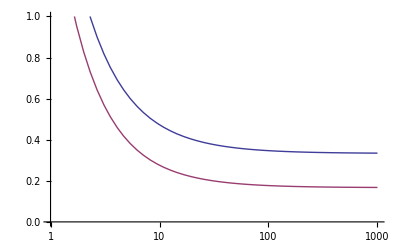

```mathematica
LogLinearPlot[{r[n,2],r[n,3]},{n,1,10^3},PlotRange->{Automatic,{0,1}},GridLines->{None,{1/3,1/6}},PlotStyle->{Thick}]
```

#### Asymptotic limits for large n: typical in practice

```mathematica
rl[p_]:=Limit[r[n,p],n->+Infinity]
rl[p]
rl[{1,2,3,4}]
```

2/(p+p^2)

{1,1/3,1/6,1/10}